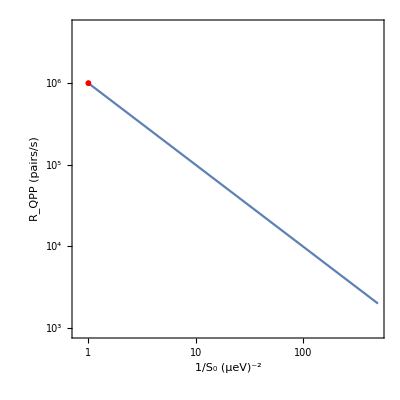

```mathematica
(* Panel D of Figure 3 of the main text *)
(* Plot dependence of decoherence rate on coefficient S_0 *)

(* we see how the results scale with S_0 using a value of R_{QPP} of 1 MHz at a value of S_0 of (1 μeV)^2 .

excitation rate scales as S *)

(* excitation rate at S_0 = 1 μeV^2 is about 1 MHz *)

ClearAll["Global`*"];



(* fix coefficient so that rate at S_0 = 1 μeV^2 is 10^6 *)
(* plot R_QPP versus 1/S^0 *)
S0inverse=1/S0;

p1=LogLogPlot[(10^6)/S0inverse,{S0inverse, 1.,500},

Axes->False,Frame->True,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameLabel->{"1/S_0 (μeV)^-2","R_QPP (pairs/s)",None,None},
PlotRange->{{0.8,500},{900,5*10^6}},
FrameTicks->{{{{1,"1"},{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"},{10^5,"10^5"},{10^6,"10^6"}},None},{{1,10,100},None}},
AspectRatio->1.,
(* ImageSize->{width,height}:Specifies absolute dimensions in points (e.g.,ImageSize->{500,300}). *)
ImageSize->{Automatic,200}(*:Fixes only the height while letting the width adjust automatically based on the content.*)
];

p2=ListLogLogPlot[{{1.,10^6}},PlotRange->{{0.8,500},{900,5*10^6}},PlotStyle->Red,PlotMarkers->{●,6}];

Show[p1,p2]
```